# Example 6.5: Random tensor networks for holographic duality

```mathematica
SetDirectory[NotebookDirectory[]];
<<RTNI`
```

Package RTNI (Random Tensor Network Integrator) version 1.0.5 (last modification: 26/01/2019).

Loading precomputed Weingarten Functions from /precomputedWG/functions1.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions2.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions3.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions4.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions5.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions6.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions7.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions8.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions9.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions10.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions11.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions12.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions13.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions14.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions15.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions16.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions17.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions18.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions19.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions20.txt

```mathematica
(* subroutine for creating tensor networks representing Tr(\rho\otimes rho) and \tr(\rho_A^2) for a given graph G and subset A of the vertices*)buildTNfromGraph[g_,marginal_,debug_:False]:=Module[{psi,nV,nE,i,e,traceRho,traceRhoASquared,newEdge,degree,v1,v2,v,psiStar,rho},
nV=Length[VertexList[g]];
nE=Length[EdgeList[g]];
degree=ConstantArray[1,nV];
psi={};
psiStar={};
For[i=1,i≤nE,i++,
e=EdgeList[g][[i]];
v1=e[[1]];
v2=e[[2]];
If[debug,Print["edge: ",v1," --- ",v2,"  read."]];
degree[[v1]]++;
degree[[v2]]++;
newEdge={{"U"<>ToString[v1],1,"out",degree[[v1]]},{"U"<>ToString[v2],1,"out",degree[[v2]]}};
AppendTo[psi,newEdge];
newEdge={{"U"<>ToString[v1]<>"*",1,"in",degree[[v1]]},{"U"<>ToString[v2]<>"*",1,"in",degree[[v2]]}};
AppendTo[psiStar,newEdge];
];
rho=Join[psi,psiStar];
traceRho=rho;
For[i=1,i≤nV,i++,
v=i;
newEdge={{"U"<>ToString[v],1,"out",1},{"U"<>ToString[v]<>"*",1,"in",1}};
AppendTo[traceRho,newEdge];
];
traceRhoASquared=cloneGraph[rho,2];
For[i=1,i≤nV,i++,
v=i;
If[MemberQ[marginal,v],
newEdge={{"U"<>ToString[v],1,"out",1},{"U"<>ToString[v]<>"*",2,"in",1}};
AppendTo[traceRhoASquared,newEdge];
newEdge={{"U"<>ToString[v],2,"out",1},{"U"<>ToString[v]<>"*",1,"in",1}};
AppendTo[traceRhoASquared,newEdge];
,
newEdge={{"U"<>ToString[v],1,"out",1},{"U"<>ToString[v]<>"*",1,"in",1}};
AppendTo[traceRhoASquared,newEdge];
newEdge={{"U"<>ToString[v],2,"out",1},{"U"<>ToString[v]<>"*",2,"in",1}};
AppendTo[traceRhoASquared,newEdge];
];
];
{cloneGraph[traceRho,2],traceRhoASquared}
];

(* routine for integrating over all unitaries by invoking integrateHaarUnitary several times *)
integrateAllUs[tn_,d_,s_,debug_:False]:=Module[{listU,i,name,v,p,maxLeg,intTN},
listU={};
maxLeg={};
For[i=1,i≤Length[tn],i++,
For[j=1,j≤2,j++,
name=Characters[tn[[i,j,1]]];
If[debug,Print[name]];
If[name[[1]]=="U"&&Last[name]≠"*",
v=ToExpression[StringJoin[name[[2;;]]]];
If[debug,Print[v]];
If[!MemberQ[listU,v],
AppendTo[listU,v];
AppendTo[maxLeg,1];
];
If[debug,Print[listU]];
p=Position[listU,v][[1,1]];
maxLeg[[p]]=Max[tn[[i,j,4]],maxLeg[[p]]];
If[debug,Print[maxLeg]];
];
]];
intTN=tn;
For[i=1,i≤Length[listU],i++,
intTN=integrateHaarUnitary[intTN,"U"<>ToString[listU[[i]]],{},Join[{d},ConstantArray[s,maxLeg[[i]]-1]],d s^(maxLeg[[i]]-1)];
];
intTN
];
(* routines for computing the averages via the Ising model formulation*)
computeenergy[spinconfig_,g_,marginal_]:=Module[{result=0,nV,nE,degree,v1,v2,v},
nV=Length[VertexList[g]];
nE=Length[EdgeList[g]];
degree=ConstantArray[1,nV];(* add energy contribution from Ising interaction *)
For[i=1,i≤nE,i++,
e=EdgeList[g][[i]];
v1=e[[1]];
v2=e[[2]];
(*Print["vertex v1=", v1," v2=",v2," energy contrib=",spinconfig[[v1]]*spinconfig[[v2]]];*)
result=result+spinconfig[[v1]]*spinconfig[[v2]];
];
(* add energy contribution from field *)
For[i=1,i≤nV,i++,
v=i; 
(*Print["vertex v=", v,"  field energy contrib=",spinconfig[[v]]*If[MemberQ[marginal,v],1,-1]];*)
result=result+spinconfig[[v]]*If[MemberQ[marginal,v],-1,1];
];
result=result/2;
result
];
findallenergies[g_,marginal_]:=Module[{spinconfiglist,nV,result,j},
nV=Length[VertexList[g]];
spinconfiglist=Tuples[{-1,1},nV];
result=Table[{spinconfiglist[[j]],computeenergy[spinconfiglist[[j]],g,marginal]},{j,1,2^nV}];
result=SortBy[result,#[[2]]&];
result
];
computeexponents[g_,marginal_]:=Module[{allspinsE,marginalspinsE,Eminall,Eminmarginal,result},
nV=Length[VertexList[g]];
allspinsE=findallenergies[g,{}];
marginalspinsE=findallenergies[g,marginal];
Emaxall=allspinsE[[Length[allspinsE]]][[2]];
Emaxmarginal=marginalspinsE[[Length[allspinsE]]][[2]];
result={Emaxall,Emaxmarginal};(*,Emaxall-Emaxmarginal,marginalspinsE[[1]]};*)
result
];
```

# Triangle graph example

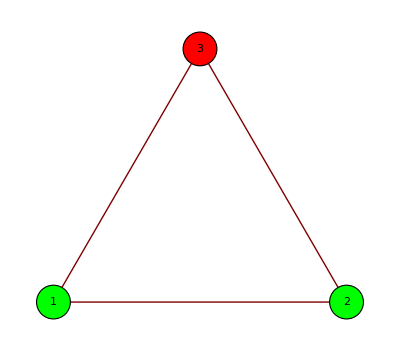

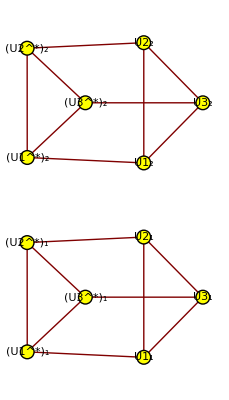

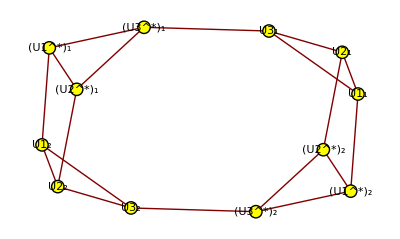

(3+(-2+d) d)/(d^7 (1+d) (1+(-1+d) d)^3)

12

(1+d^2)/(d^8 (1+d) (1+(-1+d) d)^3)

13

{3,2}

```mathematica
g=Graph[{1<->2,2<->3,3<->1}];
edgeNormalization=d^(-2EdgeCount[g]);(* This pre-factor corresponds to using normalized maximally entangled states in the main text *)
marginal={1,2};
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[marginal,#2],Green,Red],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
Export["triangle-1.pdf",%];
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
Export["triangle-2.pdf",%];
visualizeTN[tn[[2]]]
Export["triangle-3.pdf",%];
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
ZA=edgeNormalization  integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[ZA]/Log[d],d->Infinity]
computeexponents[g,marginal]
```

```mathematica
(* TO BE FIXED *)
```

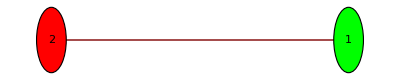

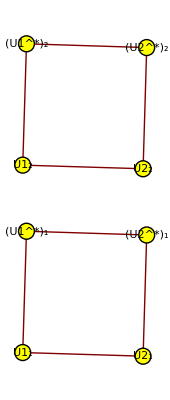

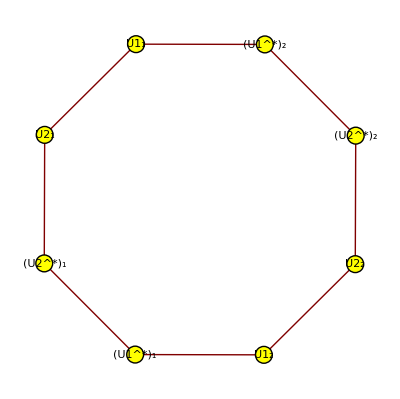

(3+d^2)/((d+d^3)^2)

4

(1+3 d^2)/(d^3 (1+d^2)^2)

5

{3/2,1/2}

```mathematica
g=Graph[{1<->2}];
edgeNormalization=d^(-2 EdgeCount[g]);
marginal={1};
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[marginal,#2],Green,Red],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
ZA=edgeNormalization  integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[ZA]/Log[d],d->Infinity]
(*renyi2=Z1/Z0//FullSimplify*)
computeexponents[g,marginal]
(*Series[renyi2/.{s->d},{d,Infinity,20}]*)
```

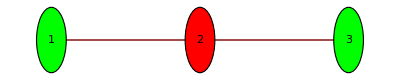

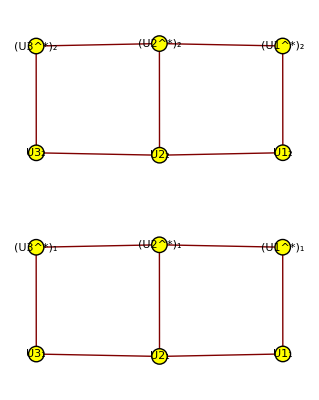

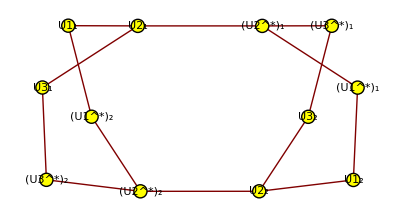

(1+d (3+(-1+d) d))/(d (1+(-1+d) d) (1+d^2)^2)

(1+d (-1+d (3+d)))/((1+(-1+d) d) (d+d^3)^2)

4

5

{5/2,3/2}

```mathematica
g=Graph[{1<->2,2<->3}];
marginal={1,3};
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[marginal,#2],Green,Red],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Z1=integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
Limit[-Log[Z1]/Log[d],d->Infinity]
computeexponents[g,marginal]
(*renyi2=Z1/Z0;
Series[renyi2,{d,Infinity,4}]
computeexponents[g,marginal]*)
```

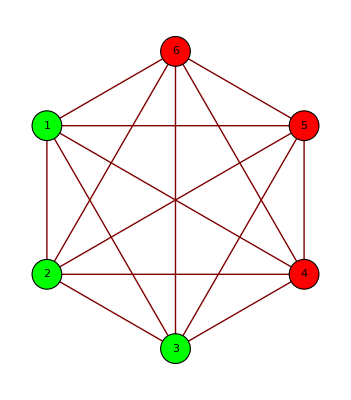

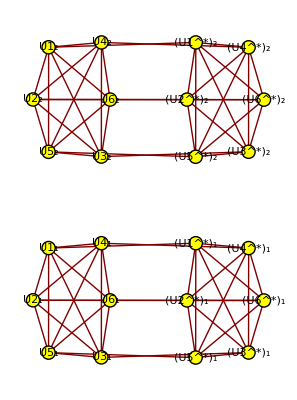

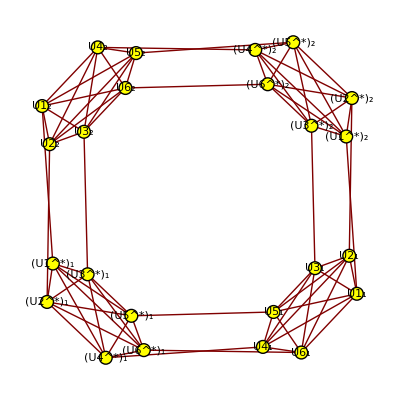

(35+21 d^2+7 d^6+d^12)/(d^8 (1+d^6)^6)

32

(1+15 d^2+27 d^4+13 d^6+6 d^8+2 d^12)/(d^11 (1+d^6)^6)

35

{21/2,15/2}

```mathematica
g=CompleteGraph[6];
marginal={1,2,3};
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[marginal,#2],Green,Red],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
Z1=edgeNormalization integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z1]/Log[d],d->Infinity]
computeexponents[g,marginal]
(*Series[Z1/Z0,{d,Infinity,3}]
computeexponents[g,marginal]*)
```

```mathematica
21-15
```

6

```mathematica
squareLatticeGraph[m_,n_]:=Module[{g,i,j},
g={};
For[i=1,i≤m,i++,
For[j=1,j≤n-1,j++,
AppendTo[g,UndirectedEdge[n(i-1)+j,n(i-1)+j+1]];
]];
For[i=1,i≤m-1,i++,
For[j=1,j≤n,j++,
AppendTo[g,UndirectedEdge[n(i-1)+j,n(i)+j]];
]];
Graph[g]
];
```

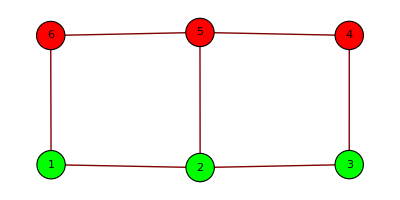

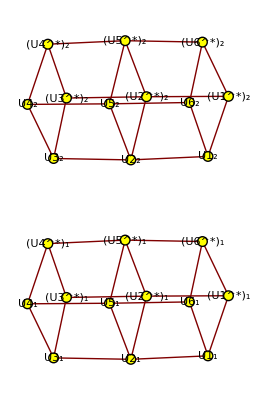

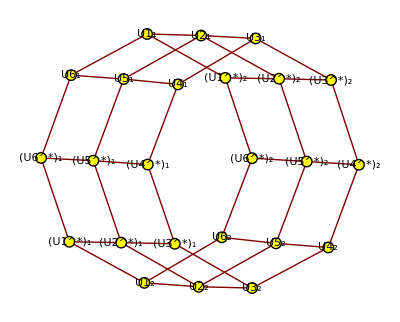

(2+d^2 (9+d (2+d+3 d^3-2 d^4+d^5)))/(d^18 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^2)

28

(1+d (-2+d (9+d^2 (3+d (2+3 d)))))/(d^19 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^2)

31

{13/2,7/2}

```mathematica
g=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,2<->5}];
edgeNormalization=d^(-2EdgeCount[g]);
marginal={1,2,3};
GraphPlot[g,VertexRenderingFunction->({If[!MemberQ[marginal,#2],Red,Green],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
Z1=edgeNormalization integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z1]/Log[d],d->Infinity]
computeexponents[g,marginal]
(*Series[Z1/Z0,{d,Infinity,3}]
computeexponents[g,marginal]*)
```

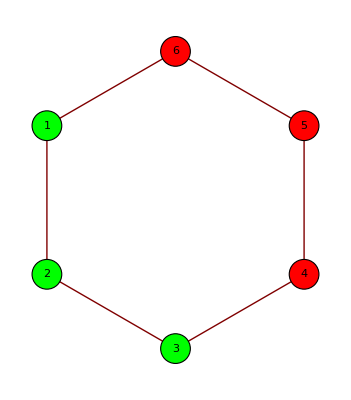

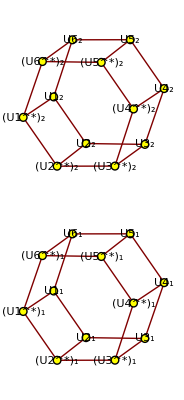

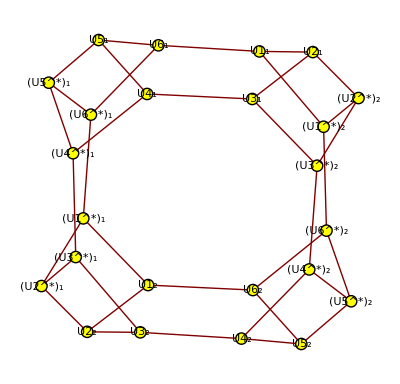

((2+(-1+d) d) (1+d (2+d (2+(-2+d) d))))/(d^15 (1+d)^3 (1+(-1+d) d)^6)

24

(1+d (-1+d (8+(-1+d) d (4+d))))/(d^16 (1+d)^3 (1+(-1+d) d)^6)

26

{6,4}

```mathematica
g=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,2<->5}];
g=EdgeDelete[g,{2<->5}];edgeNormalization=d^(-2EdgeCount[g]);
GraphPlot[g,VertexRenderingFunction->({If[!MemberQ[marginal,#2],Red,Green],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
Z1=edgeNormalization integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z1]/Log[d],d->Infinity]
computeexponents[g,marginal]
```

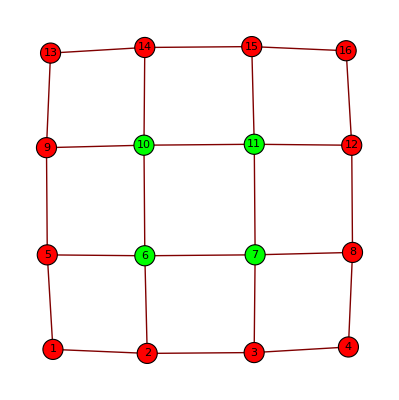

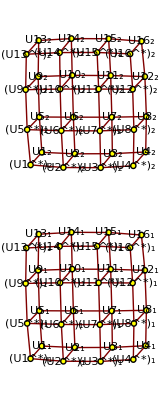

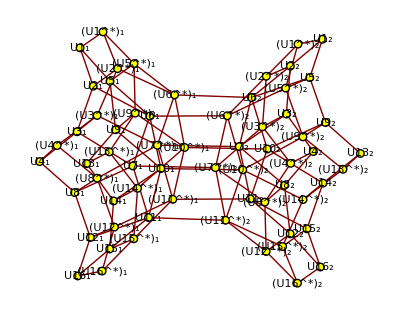

(2+d (-8+d (28+d (-36+d (82+d (-4+d (106+d (220+d (-46+d (536+d (-416+d (640+d (-324+d (116+d (294+d (-512+d (689+d (-702+d (645+d (-500+d (344+d (-204+d (110+(-4+d) d (13+(-2+d) d))))))))))))))))))))))))/(d^28 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^8 (1+(-1+d) d (1+d^2))^4)

60

(2+d (-8+d (32+d (-32+d (43+d (166+d (-139+d (400+d (-71+d (178+d (279+d (-232+d (534+d (-460+d (504+d (-328+d (239+d (-142+d (91+d (-48+d (21+(-6+d) d)))))))))))))))))))))/(d^28 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^8 (1+(-1+d) d (1+d^2))^4)

64

{20,16}

```mathematica
g=squareLatticeGraph[4,4];
marginal={6,7,10,11};
GraphPlot[g,VertexRenderingFunction->({If[!MemberQ[marginal,#2],Red,Green],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
Z1=edgeNormalization integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z1]/Log[d],d->Infinity]
(*Series[Z1/Z0,{d,Infinity,3}]*)
computeexponents[g,marginal]
```

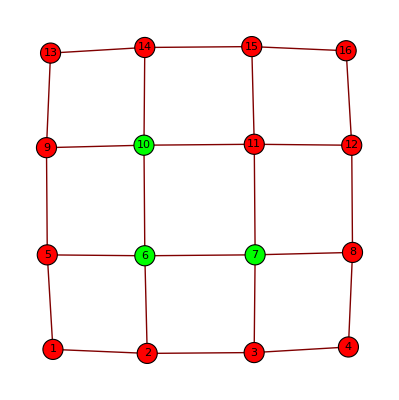

-Graphics-

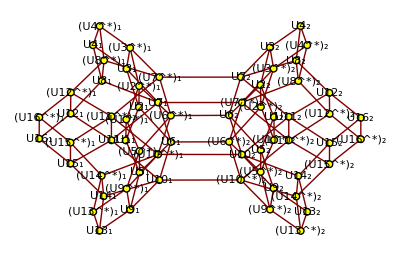

(2+d (-8+d (28+d (-36+d (82+d (-4+d (106+d (220+d (-46+d (536+d (-416+d (640+d (-324+d (116+d (294+d (-512+d (689+d (-702+d (645+d (-500+d (344+d (-204+d (110+(-4+d) d (13+(-2+d) d))))))))))))))))))))))))/(d^28 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^8 (1+(-1+d) d (1+d^2))^4)

60

(1+d (-4+d (16+d (-22+d (43+d (34+d (-32+d (296+d (-150+d (366+d (55+d (29+d (359+d (-303+d (495+d (-404+d (404+d (-300+d (229+d (-149+d (94+d (-49+d (21+(-6+d) d)))))))))))))))))))))))/(d^29 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^8 (1+(-1+d) d (1+d^2))^4)

63

{20,17}

```mathematica
g=squareLatticeGraph[4,4];
marginal={6,7,10};
GraphPlot[g,VertexRenderingFunction->({If[!MemberQ[marginal,#2],Red,Green],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
Z1=edgeNormalization integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z1]/Log[d],d->Infinity]
(*Series[Z1/Z0,{d,Infinity,3}]*)
computeexponents[g,marginal]
```

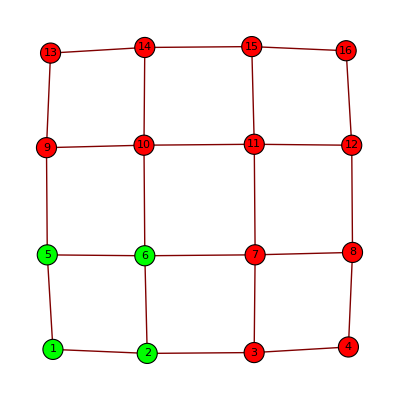

-Graphics-

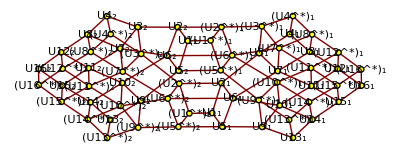

(2+d (-8+d (28+d (-36+d (82+d (-4+d (106+d (220+d (-46+d (536+d (-416+d (640+d (-324+d (116+d (294+d (-512+d (689+d (-702+d (645+d (-500+d (344+d (-204+d (110+(-4+d) d (13+(-2+d) d))))))))))))))))))))))))/(d^28 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^8 (1+(-1+d) d (1+d^2))^4)

60

(2+d (-8+d (31+d (-50+d (137+d (-111+d (289+d (8+d (92+d (441+d (-384+d (706+d (-535+d (531+d (-265+d (132+d (24+d (-61+d (71+2 d (-22+d (12+(-4+d) d)))))))))))))))))))))/(d^28 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^8 (1+(-1+d) d (1+d^2))^4)

64

{20,16}

```mathematica
g=squareLatticeGraph[4,4];
marginal={1,2,5,6};
GraphPlot[g,VertexRenderingFunction->({If[!MemberQ[marginal,#2],Red,Green],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
Z1=edgeNormalization integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z1]/Log[d],d->Infinity]
computeexponents[g,marginal]
```

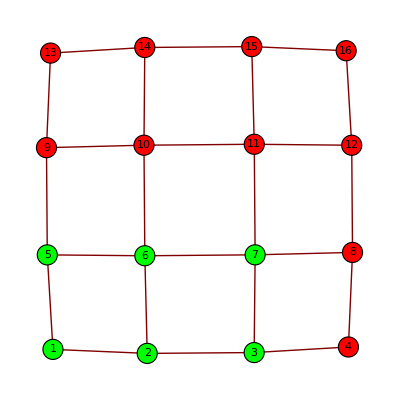

-Graphics-

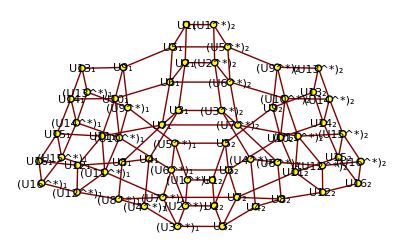

(2+d (-8+d (28+d (-36+d (82+d (-4+d (106+d (220+d (-46+d (536+d (-416+d (640+d (-324+d (116+d (294+d (-512+d (689+d (-702+d (645+d (-500+d (344+d (-204+d (110+(-4+d) d (13+(-2+d) d))))))))))))))))))))))))/(d^28 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^8 (1+(-1+d) d (1+d^2))^4)

60

(2+d (-7+d (27+d (-35+d (99+d (-32+d (174+d (124+d (6+d (474+d (-364+d (615+d (-366+d (341+d (-118+d (62+d (20+d (-9+d (9+d (2+(-1+d) d))))))))))))))))))))/(d^28 (1+d)^2 (1+(-1+d) d)^4 (1+d^4)^8 (1+(-1+d) d (1+d^2))^4)

65

```mathematica
g=squareLatticeGraph[4,4];
marginal={1,2,3,5,6,7};
GraphPlot[g,VertexRenderingFunction->({If[!MemberQ[marginal,#2],Red,Green],EdgeForm[Black],Disk[#,.1],Black,Text[#2,#1]}&)]
tn=buildTNfromGraph[g,marginal];
visualizeTN[tn[[1]]]
visualizeTN[tn[[2]]]
Z0=edgeNormalization integrateAllUs[tn[[1]],d,d][[1,2]]//FullSimplify
Limit[-Log[Z0]/Log[d],d->Infinity]
ZA=edgeNormalization integrateAllUs[tn[[2]],d,d][[1,2]]//FullSimplify
Limit[-Log[ZA]/Log[d],d->Infinity]
```

```mathematica
computeexponents[g,marginal]
```

{20,15}